```mathematica
Clear[ndf,pdf,cdf]
ndf[θ_,α_]:=α^2/(π*(Cos[θ]^2*(α^2-1)+1)^2)
(*cdf=Function[{θ,α},Evaluate[Integrate[2*π*ndf[θ,α]*Cos[θ]*Sin[θ],θ]]]*)
cdf[θ_,α_]:=(1-Cos[θ]^2)/(1+Cos[θ]^2*(α^2-1))
pdf[θ_,α_]:=ndf[θ,α]*Cos[θ]
pdfCos[cosθ_,α_]:=α^2/(π*(cosθ^2*(α^2-1)+1)^2)*cosθ
```

Mip Expression

```mathematica
mipMax=8;
(*mu[mip_]:=1-1/3 2^(2(mip-mipMax))   Solid angles yields θ > π/2*)
mu[mip_]:=1/(√(1+2^(2(mip-mipMax))))

mu[8]
2*ArcCos[mu[8]]
```

1/(√2)

π/2

Compute the correlation between 2 neighbor NDFs separated by θ

Here we have 2 lobes aligned along 2 directions separated by an angle θ and we need to find the correlation least correlation between the 2 although there must be a little correlation anyway otherwise we could always choose roughness 0 for maximization.

It would look like we’re doing the same thing all over again but the normalization by pdf(0,α) makes much more sense than dividing by the cdf!

Showing angular correlation visually:

```mathematica
correl[θ_,α_,θ0_]:=Max[0,Min[pdf[θ,α],pdf[θ0-θ,α]]]/pdf[0,α]
correl[θ_,α_,θ0_]:=(pdf[θ,α]*pdf[θ0-θ,α])/pdf[0,α]^2
Manipulate[ParametricPlot[ { 4*θ*{1,Tan[π/2-θ0]},{Sin[θ],Cos[θ]},4*θ*{Tan[θ0/2],1},
pdf[θ,α]/pdf[0,α]*{Sin[θ],Cos[θ]},
pdf[θ0-θ,α]/pdf[0,α]*{Sin[θ],Cos[θ]},
correl[θ,α,θ0]*{Sin[θ],Cos[θ]},
(*(1/(√2))^2*{Sin[θ],Cos[θ]}*)
},{θ,-π/2,π/2},PlotRange->{{-1,1},{0,1}},PlotStyle->{LightGray,LightGray,Orange,defaultBlue,defaultBlue,Red,Green}],{{α,0.1},0,1},{{θ0,π/2},0,π/2}]
```

Plotting angular correlation as a function of angle:

```mathematica
Manipulate[Show[Plot[correl[θ,α,θ0],{θ,0,θ0},PlotRange->{0,Full}],ParametricPlot[{θ0/2,t},{t,-100,100},PlotStyle->Red],ParametricPlot[{t,(1/(√2))^2},{t,0,θ0},PlotStyle->Red]],{{θ0,π/10},0,π/2},{{α,0.1},0,1}]
```

```mathematica
correl[π/4,1,π/2]
```

1/2

## Finding a Mapping

So okay, we can accept a certain amount of correlation that is given by the value at θ_0/2when α=1 and θ_0=π/2
Now we can find the roughness for a given θ_0 :

	c=((pdf(θ_0/2,α))/(pdf(0,α)))^2

We can totally get rid of the squaring and rewrite the same expression for a new c.

By fixing c = (pdf(π/4,1))/(pdf(0,1)) corresponding to the correlation of the worst mip that sees a π/2 angle (a full face of the cube) and must correspond to the roughness value α=1.

We find:	c=1/(√2)

```mathematica
(ndf[π/4,1]*Cos[π/4])/pdf[0,1]
pdf[π/4,1]/pdf[0,1]
```

1/(√2)

1/(√2)

```mathematica
Clear[c,θ,α]
(*Solve[pdf[θ,α]/pdf[0,α]==c,α]*)
Solve[(α^4*b)/((b^2(α^2-1)+1)^2)==c,α]
```

{{α→-√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)-(√(b (-1+b^2)^2 c))/(-b+b^4 c))},{α→√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)-(√(b (-1+b^2)^2 c))/(-b+b^4 c))},{α→-√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)+(√(b (-1+b^2)^2 c))/(-b+b^4 c))},{α→√(-(b^2 c)/(-b+b^4 c)+(b^4 c)/(-b+b^4 c)+(√(b (-1+b^2)^2 c))/(-b+b^4 c))}}

Unfortunately, it’s impossible to invert the result...

```mathematica
(*Solve[(α^4*b)/((b^2(α^2-1)+1)^2)==c,b]*)
```

```mathematica
sqAlpha:=Function[θ,
μ=Cos[θ];
c=1/(√2);
(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
]
sqAlphaMu[μ_]:=(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
```

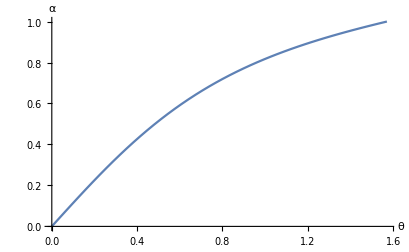

```mathematica
Plot[√sqAlpha[θ/2],{θ,0,π/2},PlotRange->{0,1},AxesLabel->{"θ","α"}]
```

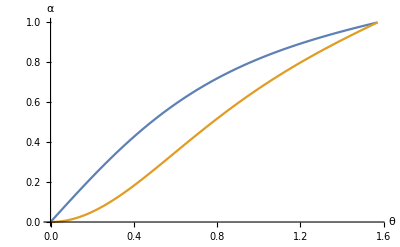

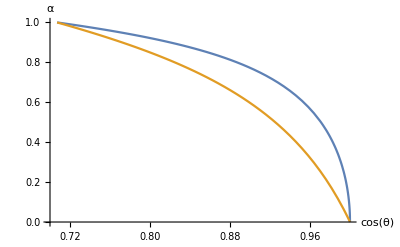

```mathematica
Plot[{√sqAlpha[θ/2],sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1},AxesLabel->{"θ","α"}]
Plot[{√sqAlphaMu[μ],sqAlphaMu[μ]},{μ,1/(√2),1},PlotRange->{{0.70,1},{0,1}},AxesLabel->{"cos(θ)","α"}]
```

2/3

1.68214

{0.00733224,0.0146636,0.0293201,0.0585836,0.116718,0.229944,0.434916,0.731737,1.02718}

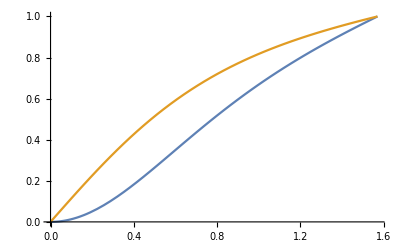

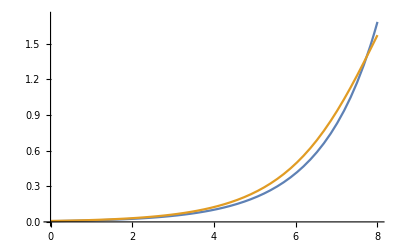

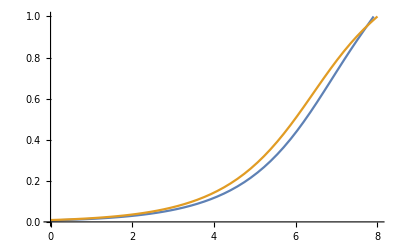

```mathematica
mipMax=8;
mu2[mip_]:=1/(√(1+2^(2(mip-mipMax))))
mu[mip_]:=1-1/3 2^(2(mip-mipMax))   (*Solid angles yields θ > π/2*)
sqRoughnessFromMip[mip_]:=sqAlpha[ArcCos[mu[mip]] ]
sqRoughnessFromMip2[mip_]:=sqAlpha[ArcCos[mu2[mip]] ]
mu[8]
N[2*ArcCos[mu[8]]]
Table[N[√sqRoughnessFromMip[mip]],{mip,0,mipMax}]
Plot[{sqAlpha[θ/2],√sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1}]
Plot[{2*ArcCos[mu[mip]],2*ArcCos[mu2[mip]]},{mip,0,mipMax},PlotRange->{0,1.1*π/2}]
Plot[{√sqRoughnessFromMip[mip],√sqRoughnessFromMip2[mip]},{mip,0,mipMax},PlotRange->{0,1}]
```

```mathematica
Manipulate[ParametricPlot[ { 4*θ*{1,Tan[π/4-θ0/2]},4*θ*{1,Tan[π/4+θ0/2]},{Sin[θ],Cos[θ]},4*θ*{1,1},
pdf[Abs[θ-(π/4-θ0/2)],√sqAlpha[θ0/2]]/pdf[0,√sqAlpha[θ0/2]]*{Sin[θ],Cos[θ]},
pdf[Abs[(π/4+θ0/2)-θ],√sqAlpha[θ0/2]]/pdf[0,√sqAlpha[θ0/2]]*{Sin[θ],Cos[θ]},
(pdf[Abs[θ-(π/4-θ0/2)],√sqAlpha[θ0/2]]*pdf[Abs[(π/4+θ0/2)-θ],√sqAlpha[θ0/2]])/pdf[0,√sqAlpha[θ0/2]]^2*{Sin[θ],Cos[θ]},
(1/(√2))^2*{Sin[θ],Cos[θ]}
},{θ,0,π/2},PlotRange->{{0,1},{0,1}},PlotStyle->{LightGray,LightGray,LightGray,Orange,defaultBlue,defaultBlue,Red,Green}],{{θ0,π/2},0.001,π/2}]
```

```mathematica
Manipulate[ParametricPlot[ { 4*θ*{1,Tan[π/2-θ0]},{Sin[θ],Cos[θ]},4*θ*{Tan[θ0/2],1},
pdf[θ,√sqAlpha[θ0/2]]/pdf[0,√sqAlpha[θ0/2]]*{Sin[θ],Cos[θ]},
pdf[θ0-θ,√sqAlpha[θ0/2]]/pdf[0,√sqAlpha[θ0/2]]*{Sin[θ],Cos[θ]},
correl[θ,√sqAlpha[θ0/2],θ0]*{Sin[θ],Cos[θ]},
(1/(√2))^2*{Sin[θ],Cos[θ]}
},{θ,-π/2,π/2},PlotRange->{{-1,1},{0,1}},PlotStyle->{LightGray,LightGray,Orange,defaultBlue,defaultBlue,Red,Green}],{{θ0,π/2},0.001,π/2}]
```

Fitting

The expression to get μ from roughness is a nightmare to invert so let’s do a curve fitting instead...

{{1.,0.707107},{0.995845,0.710036},{0.991663,0.712965},{0.987454,0.715894},{0.983216,0.718823},{0.978948,0.721751},{0.97465,0.72468},{0.970321,0.727609},{0.965958,0.730538},{0.961562,0.733467},{0.957132,0.736396},{0.952665,0.739325},{0.948161,0.742254},{0.943619,0.745183},{0.939037,0.748112},{0.934415,0.751041},{0.92975,0.75397},{0.925042,0.756899},{0.920289,0.759828},{0.915489,0.762756},{0.910642,0.765685},{0.905746,0.768614},{0.900799,0.771543},{0.895799,0.774472},{0.890746,0.777401},{0.885636,0.78033},{0.880469,0.783259},{0.875243,0.786188},{0.869956,0.789117},{0.864605,0.792046},{0.859189,0.794975},{0.853706,0.797904},{0.848154,0.800833},{0.84253,0.803762},{0.836832,0.80669},{0.831058,0.809619},{0.825206,0.812548},{0.819272,0.815477},{0.813254,0.818406},{0.80715,0.821335},{0.800956,0.824264},{0.794669,0.827193},{0.788287,0.830122},{0.781806,0.833051},{0.775224,0.83598},{0.768535,0.838909},{0.761738,0.841838},{0.754828,0.844767},{0.747801,0.847696},{0.740653,0.850624},{0.73338,0.853553},{0.725978,0.856482},{0.718442,0.859411},{0.710767,0.86234},{0.702948,0.865269},{0.694979,0.868198},{0.686856,0.871127},{0.678573,0.874056},{0.670123,0.876985},{0.6615,0.879914},{0.652698,0.882843},{0.64371,0.885772},{0.634528,0.888701},{0.625144,0.89163},{0.615552,0.894558},{0.605741,0.897487},{0.595704,0.900416},{0.58543,0.903345},{0.574911,0.906274},{0.564135,0.909203},{0.553092,0.912132},{0.541769,0.915061},{0.530155,0.91799},{0.518237,0.920919},{0.506001,0.923848},{0.493432,0.926777},{0.480515,0.929706},{0.467234,0.932635},{0.45357,0.935563},{0.439506,0.938492},{0.425022,0.941421},{0.410097,0.94435},{0.394707,0.947279},{0.37883,0.950208},{0.36244,0.953137},{0.345509,0.956066},{0.328008,0.958995},{0.309905,0.961924},{0.291167,0.964853},{0.271756,0.967782},{0.251635,0.970711},{0.23076,0.97364},{0.209086,0.976569},{0.186564,0.979497},{0.163139,0.982426},{0.138754,0.985355},{0.113346,0.988284},{0.0868448,0.991213},{0.0591763,0.994142},{0.030258,0.997071},{0.,1.}}

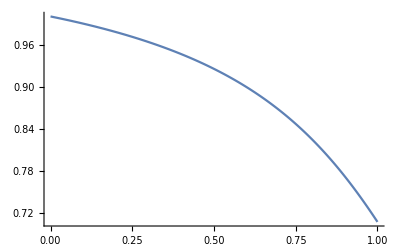

```mathematica
data=Table[{ N[sqAlphaMu[μ]],N[μ]},{μ,1/(√2),1,(1-1/(√2))/100}]
ListLinePlot[data,PlotRange->Full]
```

(a+b x+c x^2)/(d+e x+f x^2)

(a+b x+c x^2)/(a+e x+f x^2)

Function[x,(1.2547-1.87042 x+0.720235 x^2)/(1.2547-1.75224 x+0.645329 x^2)]

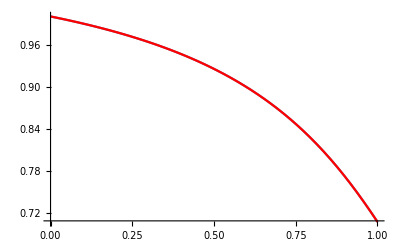

1.00011

```mathematica
Clear[a,b,c,d,e,f]
model=(a+b*x+c*x^2)/(d+e*x+f*x^2)
model=(a+b*x+c*x^2)/(a+e*x+f*x^2)

fCos2Roughness2D=Function[x,Evaluate[model/.FindFit[data,model,{a,b,c,d,e,f},x]]]
Show[ListLinePlot[data,PlotRange->{1/(√2),1}],Plot[fCos2Roughness2D[x],{x,0,1},PlotStyle->Red]]
√2 fCos2Roughness2D[1]
```

3D Lobes Inter-Penetration Modeling

We’re starting over again but this time measuring the ratio of volume that get interpenetrated depending on the angle between lobes.
We know a volume element is given by dV=r^2 sin(θ) dr dθ dϕ and the volume integral is:

	I=∫_-π^π ∫_0^(π/2) ∫_0^(r(θ,ϕ,α)) r^2 sin(θ)ⅆθⅆϕ=∫_-π^π ∫_0^(π/2) 1/3(r(θ,ϕ,α))^3 sin(θ)ⅆθⅆϕ

In one case, we’re looking for the entire volume so r(θ,ϕ,α)=r(θ )=(D(θ,α))/π cos(θ) the BRDF’s normal distribution function times the cosine of the angle.
In the second case we’re looking for the intersection of 2 volumes and r(θ,ϕ,α)=r(θ )=min( D(θ,α) cos(θ), D(θ',α) cos(θ') ).

Here, cos(θ')= sin( θ ) cos( ϕ ) sin( θ_0) + cos( θ ) cos( θ_0 ) and θ_0 is the cone’s aperture angle.

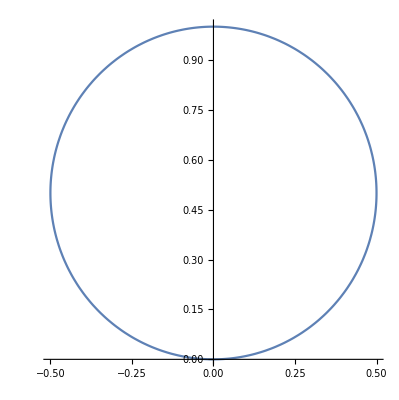

```mathematica
ParametricPlot[Cos[θ]*{Sin[θ],Cos[θ]},{θ,-π/2,π/2}]
```

```mathematica
cosAngleChange[θ_,ϕ_,γ_]:=Sin[θ]*Cos[ϕ]*Sin[γ]+Cos[θ]*Cos[γ]
penelobe[θ_,ϕ_,γ_,α_]:=π*Max[0,Min[pdf[θ,α],pdfCos[cosAngleChange[θ,ϕ,γ],α]]]
Manipulate[(2π)/3*NIntegrate[Cos[θ]^3*Sin[θ],{θ,0,π/2}],{{α,1},0.001,1}]
Manipulate[(2π)/3*NIntegrate[(π*pdf[θ,α])^3*Sin[θ],{θ,0,π/2}],{{α,1},0.001,1}]
Manipulate[1/3 NIntegrate[penelobe[θ,ϕ,θ0,α]^3*Sin[θ],{θ,0,π/2},{ϕ,-π,π}],{{α,1},0.001,1},{{θ0,π/2},0,π/2}]
```

NIntegrate::inumr: The integrand penelobe[θ, ϕ, 0, 1]^3\ Sin[θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1.5708}, {-3.14159, 3.14159}}.

```mathematica
SetDirectory["D:\\Workspaces\\Patapom.com\\Web\\blog\\patapom\\docs\\BRDF"]; 
countX=128;
countY=64;
fileName="VolumeInterPenetrationProper_"<>ToString[countX]<>"x"<>ToString[countY]<>".csv"
```

VolumeInterPenetrationProper_128x64.csv

```mathematica
ta=ParallelTable[{N[θ0],N[α],
1/3 NIntegrate[penelobe[θ,ϕ,θ0,α]^3*Sin[θ],{θ,0,π/2},{ϕ,-π,π}, PrecisionGoal->2,MaxRecursion->4,WorkingPrecision->$MachinePrecision]
}
,{θ0,0,π/2,(π/2)/countX}
,{α,0.001,1,(1-0.001)/countY}]
Export[fileName,ta,"CSV"];
```

```mathematica
ta2=Import[fileName,"CSV"];
ta2=ToExpression[ta2]
```

{1}
 |  |  |  |

Let’s create a normalized table by dividing by the total lobe volume

```mathematica
ta2[[129]][[65]]
```

{1.5708,1.,0.0607455145722376}

```mathematica
lobeVolume[α_]:=(2π)/3*NIntegrate[(π*pdf[θ,α])^3*Sin[θ],{θ,0,π/2}]
taLobeVolumes=Table[lobeVolume[0.001+(1-0.001)/countY*y],{y,0,countY}]
```

{2.0944×10^11,2.75255×10^6,194519.,40093.2,12971.4,5389.63,2626.56,1429.79,844.278,530.619,350.364,240.801,171.085,125.001,93.5389,71.4576,55.5842,43.9314,35.2171,28.592,23.4804,19.4838,16.3211,13.7908,11.746,10.0784,8.70686,7.56996,6.62073,5.82284,5.14795,4.57376,4.08256,3.66021,3.29529,2.97858,2.70253,2.46095,2.24873,2.06164,1.89613,1.74926,1.61851,1.5018,1.39731,1.30354,1.21917,1.14308,1.07431,1.01202,0.955491,0.904091,0.857271,0.81455,0.775507,0.739771,0.707016,0.676953,0.649327,0.623909,0.600498,0.578915,0.558997,0.540602,0.523599}

```mathematica
taNorm=Table[ta2[[x]][[y]]*{1,1,1/taLobeVolumes[[y]]},{x,1,countX+1},{y,1,countY+1}]
ref=taNorm[[countX+1]][[countY+1]][[3]]
```

{{{0.,0.001,0.999981},{0.,0.0166094,0.999733},{0.,0.0322188,0.999904},{0.,0.0478281,1.00001},{0.,0.0634375,0.999932},{0.,0.0790469,1.02913},{0.,0.0946563,1.00004},{0.,0.110266,1.00002},{0.,0.125875,0.999904},{0.,0.141484,0.999965},{0.,0.157094,0.999989},44,{0.,0.859516,0.999989},{0.,0.875125,0.999994},{0.,0.890734,0.999998},{0.,0.906344,1.},{0.,0.921953,1.},{0.,0.937563,1.},{0.,0.953172,1.},{0.,0.968781,1.},{0.,0.984391,0.99985},{0.,1.,1.}},127,{1}}
 |  |  |  |

0.116015

```mathematica
Show[ListPlot3D[Flatten[taNorm,1],PlotRange->{0,1},AxesLabel->{"θ","α","Lobe Penetration Ratio"}],Plot3D[ref,{x,0,π/2},{y,0,1},PlotStyle->Directive[Green,Opacity[0.5]]]]
```

-Graphics3D-

```mathematica
ListInterpolation[Table[taNorm[[1]][[y]][[3]],{y,1,countY+1}],{0,1}]
```

InterpolatingFunction[{{0., 1.}}, <>]

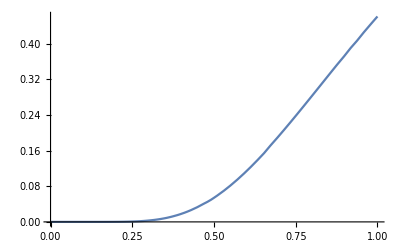

0.116015

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{α→0.602346}}

```mathematica
Clear[α]
taRoughnessFunctions=Table[ListInterpolation[Table[taNorm[[θ0]][[y]][[3]],{y,1,countY+1}],{0,1}],{θ0,1,countX+1}];
Plot[taRoughnessFunctions[[64]][α],{α,0,1}]
ref
NSolve[taRoughnessFunctions[[64]][α]==ref,α]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

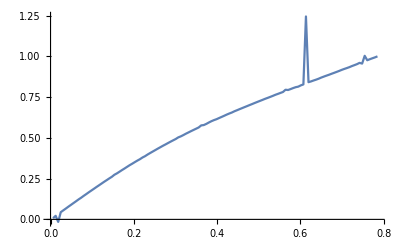

```mathematica
Clear[α]
roughnessMap=Table[{N[(θ0-1)/countX*π/4],α/.NSolve[taRoughnessFunctions[[θ0]][α]==ref,α][[1]]},{θ0,2,countX+1}];
roughnessMapCos=Table[{N[Cos[(θ0-1)/countX*π/4]],α/.NSolve[taRoughnessFunctions[[θ0]][α]==ref,α][[1]]},{θ0,2,countX+1}];
ListLinePlot[roughnessMap]
```

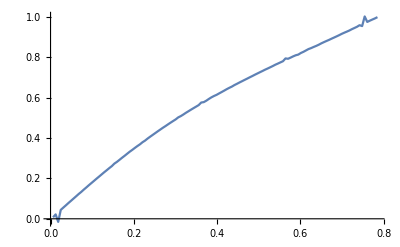

```mathematica
roughnessMap=Delete[roughnessMap,100];
roughnessMapCos=Delete[roughnessMapCos,100];
ListLinePlot[roughnessMap]
```

Let’s fit this...

{a→1.,b→2.00492,c→0.161163,d→1.,e→0.87451,f→1.}

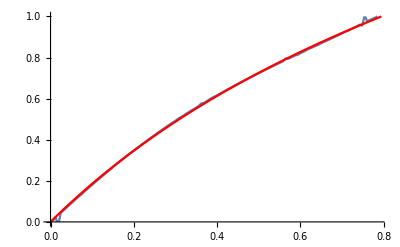

```mathematica
Clear[a,b,c,d,e,f,x,model]
model=0+b*x+c*x^2+d*x^3+e*x^4+f*x^5;
model=(0+b*x+c*x^2)/(1+e*x+0*f*x^2);
FindFit[roughnessMap,model,{a,b,c,d,e,f},x]
f2=Function[x,Evaluate[model/.FindFit[roughnessMap,model,{a,b,c,d,e,f},x]]];
Show[ListLinePlot[roughnessMap,PlotRange->{0,1}],Plot[f2[x],{x,0,π/2},PlotRange->{0,1},PlotStyle->Red]]
```

```mathematica
Sum[(f2[roughnessMap[[i]][[1]]] - roughnessMap[[i]][[2]])^2,{i,1,Length[roughnessMap]}]
```

0.00607441

Let’s plot and compare with the 2D model

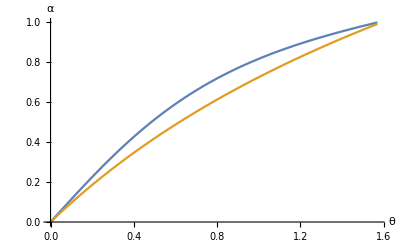

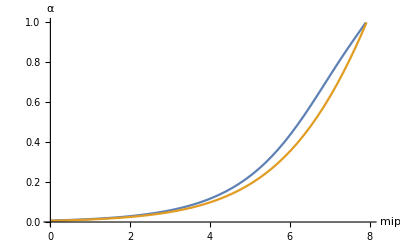

```mathematica
c=1/(√2);
sqAlpha:=Function[θ,
μ=Cos[θ];
(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
]
sqAlphaMu[μ_]:=(μ^4*c-μ^2*c-√(μ*(1-μ^2)^2*c))/(μ^4*c-μ)
sqRoughnessFromMip[mip_]:=sqAlphaMu[mu[mip]] 
sqRoughnessFromMip3D[mip_]:=f2[mu[mip]]^2
sqRoughnessFromMip3D[mip_]:=f2[ArcCos[mu[mip]]]^2
(*Plot[{sqAlpha[θ/2],√sqAlpha[θ/2]},{θ,0,π/2},PlotRange->{0,1}]*)
Plot[{sqAlpha[θ/2]^(1/2),f2[θ/2]},{θ,0,π/2},PlotRange->{0,1},AxesLabel->{"θ","α"}]
Plot[{√sqRoughnessFromMip[mip],√sqRoughnessFromMip3D[mip]},{mip,0,mipMax},PlotRange->{0,1},AxesLabel->{"mip","α"}]
```

Let’s map the inverse function now:

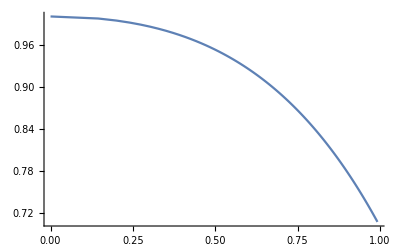

```mathematica
data=Table[{ N[f2[ArcCos[μ]]],N[μ]},{μ,1/(√2),1,(1-1/(√2))/100}];
ListLinePlot[data,PlotRange->Full]
```

(a+b x+c x^2)/(d+e x+f x^2)

(a+b x+c x^2)/(a+e x+f x^2)

Function[x,(29.0706-22.8918 x+2.3001 x^2)/(29.0706-22.8935 x+5.92586 x^2)]

7.69793×10^-11

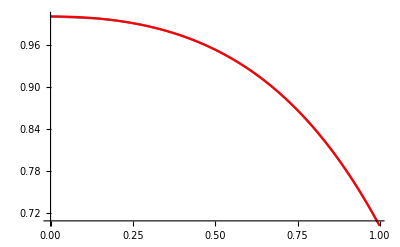

0.990744

```mathematica
Clear[a,b,c,d,e,f]
model=(a+b*x+c*x^2)/(d+e*x+f*x^2)
model=(a+b*x+c*x^2)/(a+e*x+f*x^2)
f3=Function[x,Evaluate[model/.FindFit[data,model,{a,b,c,d,e,f},x]]]
Sum[(f3[data[[i]][[1]]] - data[[i]][[2]])^2,{i,1,Length[data]}]
Show[ListLinePlot[data,PlotRange->{1/(√2),1}],Plot[f3[x],{x,0,1},PlotStyle->Red]]
√2 f3[1]
```

Let’s plot and compare with the 2D model:

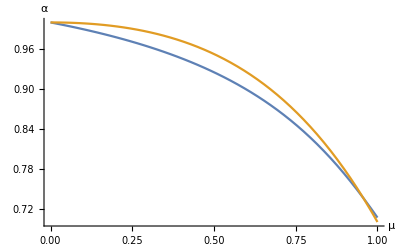

```mathematica
Plot[{f0[μ],f3[μ]},{μ,0,1},AxesLabel->{"μ","α"}]
```

Show a plot of mip level as a function of roughness

```mathematica
cosAngleChange[θ_,ϕ_,γ_]:=Sin[θ]*Cos[ϕ]*Sin[γ]+Cos[θ]*Cos[γ]
```

Let’s map the inverse function now:

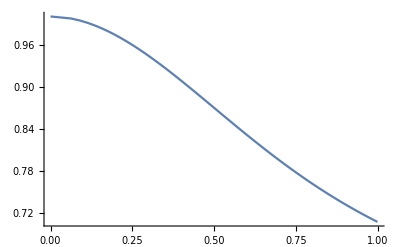

```mathematica
data=Table[{ N[f2[ArcCos[μ]]],N[μ]},{μ,1/(√2),1,(1-1/(√2))/100}];
ListLinePlot[data,PlotRange->Full]
```

(a+b x+c x^2)/(d+e x+f x^2)

(a+b x+c x^2)/(a+e x+f x^2)

Function[x,(14.0653-3.07501 x+10.5404 x^2)/(14.0653-2.91058 x+19.3144 x^2)]

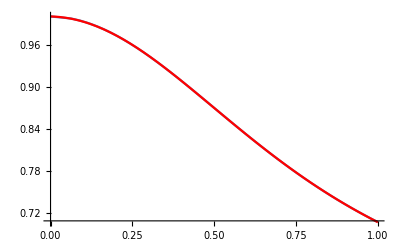

0.99934

```mathematica
Clear[a,b,c,d,e,f]
model=(a+b*x+c*x^2)/(d+e*x+f*x^2)
model=(a+b*x+c*x^2)/(a+e*x+f*x^2)
f3=Function[x,Evaluate[model/.FindFit[data,model,{a,b,c,d,e,f},x]]]
Show[ListLinePlot[data,PlotRange->{1/(√2),1}],Plot[f3[x],{x,0,1},PlotStyle->Red]]
√2 f3[1]
```

Let’s plot and compare with the 2D model:

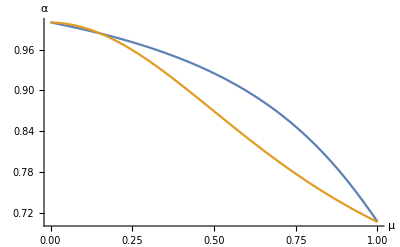

```mathematica
Plot[{f0[μ],f3[μ]},{μ,0,1},AxesLabel->{"μ","α"}]
```